```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
noise=Import["res_bc_fm_noise.csv"];
```

```mathematica
nnoise=Import["res_bc_fm_nnoise.csv"];
```

```mathematica
StandardDeviation[x]
```

0.0747036

```mathematica
x=noise[[2;;,2]];
y=nnoise[[2;;,2]];
```

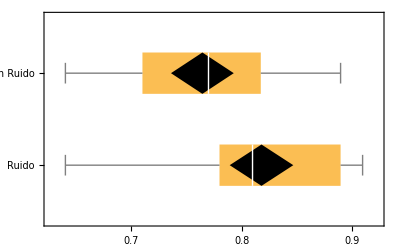

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

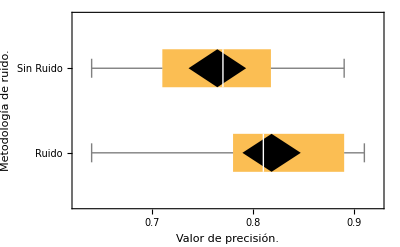

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC FeatureMap]}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export["distributions_credit_fm.pdf",%]
```

distributions_credit_fm.pdf

```mathematica
With[
{α=0.05,x=noise[[2;;,1]],
y=nnoise[[2;;,1]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 1 | 1.02725×10^-15

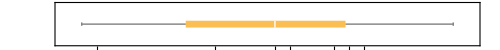

```mathematica
With[{data=nnoise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw1=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

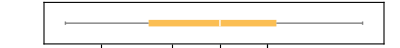

```mathematica
Show[bw1,ImageSize->Full]
```

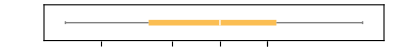

```mathematica
Show[bw1,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Sin ruido)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distrq_fm_sinruido_credit.pdf",%]
```

distrq_fm_sinruido_credit.pdf

```mathematica
SystemOpen["img.pdf"]
```

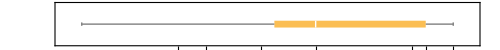

```mathematica
With[{data=noise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw2=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

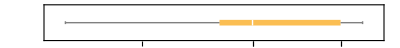

```mathematica
Show[bw2,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Ruido de Pauli)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "fm_ruido_credit.pdf",%]
```

fm_ruido_credit.pdf

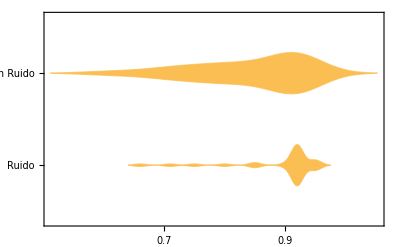

```mathematica
DistributionChart[{x,y},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```